## Construct and Parameterize One Enzyme Module

```mathematica
Quit[]
```

## Initializing the Notebook

```mathematica
<<Toolbox`';
Get["MASSef`"];
Get["MASSef`"];
```

```mathematica
SetDirectory[NotebookDirectory[]];
rxnName="TALA2";
fitLabel=rxnName;
dataFileName=rxnName;
KeqEquilibrator=1/1.19;

assumedUncertaintyFraction = 0.05;
removeInputFiles = True;
removeOutputFiles = True;
(* user will need to change this path *)
pathMASSFittingPackage = "/home/mrama/Dropbox/test bla/MASSef/";

mainFolder = "fit_TALA2";
{workingDir, pathData, runFitScriptPath, inputPath, outputPath, bigg2equilibrator}=initializeNotebook[pathMASSFittingPackage, mainFolder, removeInputFiles, removeOutputFiles];
```

Working dir:/home/mrama/Dropbox/test bla/MASSef/examples/

## Import Data

```mathematica
enzymeDataPath = FileNameJoin[{pathData, "kinetic_data.csv"}, OperatingSystem->$OperatingSystem];
bufferInfoDataPath = FileNameJoin[{pathData, "buffer_info.csv"}, OperatingSystem->$OperatingSystem];
ionChargeDataPath = FileNameJoin[{pathData, "ion_charge.csv"}, OperatingSystem->$OperatingSystem];

{rxn, mechanism, structure, nActiveSites, nAllostericSites, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList}=getEnzymeData[rxnName, enzymeDataPath, assumedUncertaintyFraction];

bufferInfo = getBufferInfoData[bufferInfoDataPath];
ionCharge = getIonData[ionChargeDataPath];

inhibitorMet={};
affectedMets={};(*There can be multiple metabolites*)
```

## Construct Module and Set Up Comparison Equations

### Print Module Dependent Information

```mathematica
printEnzymeData[rxn, mechanism, structure, nActiveSites, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList];
```

(e4p^c+f6p^c⇌g3p^c+s7p^c)^TALA2

Ping Pong Bi Bi; [f6p,g3p,e4p,s7p]

Structure: 2

Active sites: 2

Km Values:

Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
g3p | 0.000038 | 0.0000361
0.0000399 |  | M | 8.5 | 30 | glygly | 0.05 | 
e4p | 0.00009 | 0.0000855
0.0000945 |  | M | 8.5 | 30 | glygly | 0.05 | 
r5p | 0.031 | 0.02945
0.03255 |  | M | 8.5 | 30 | glygly | 0.05 | 
f6p | 0.0012 | 0.00114
0.00126 |  | M | 8.5 | 30 | glygly | 0.05 | 
s7p | 0.000285 | 0.00027075
0.00029925 |  | M | 8.5 | 30 | glygly | 0.05 |

S0.5 Values:

Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
f6p | Null
e4p | 0.002 | 71.4 | 67.83
74.97 | 1/s | 8.5 | 30 | glygly | 0.05 | 
e4p | Null
f6p | 0.05 | 79.4 | 75.43
83.37 | 1/s | 8.5 | 30 | glygly | 0.05 |

Inhibition Values:

Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
Kic | pi | 0.019 | 0.016
0.022 |  | Competitive | f6p | 0.0012
Competitive | e4p | 0.00009
Competitive | s7p | 0.000285
Competitive | g3p | 0.000038 | M | 8.5 | 30 | glygly | 0.05 |

Activation Values:

Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Parameter_Type | Metabolite | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

### Construct enzyme module

```mathematica
{{"Ping Pong Bi Bi"}, {"\"[f6p,g3p,e4p,s7p]\""}}
```

```mathematica
catalyticBranch={"E_TALA2[c] + f6p[c] <=> E_TALA2[c]&f6p",
				"E_TALA2[c]&f6p <=> E_TALA2[c]&mod&g3p",
				"E_TALA2[c]&mod&g3p <=> E_TALA2[c]&mod + g3p[c]",
                                      "E_TALA2[c]&mod + e4p[c] <=> E_TALA2[c]&mod&e4p",
				"E_TALA2[c]&mod&e4p <=> E_TALA2[c]&s7p",
				"E_TALA2[c]&s7p <=> E_TALA2[c] + s7p[c]"};


enzymeModel=constructEnzymeModule[Mechanism->catalyticBranch,Activators->{},ActivationSites->0,Inhibitors->{},InhibitionSites->0];
enzymeModel["Reactions"]
```

{((TALA2^c)_^+f6p^c⇌(TALA2^c&f6p^c)_^)^TALA21,((TALA2^c&s7p^c)_^⇌(TALA2^c)_^+s7p^c)^TALA22,((TALA2^c&mod^c)_^+e4p^c⇌(TALA2^c&mod^c&e4p^c)_^)^TALA23,((TALA2^c&f6p^c)_^⇌(TALA2^c&mod^c&g3p^c)_^)^TALA24,((TALA2^c&mod^c&e4p^c)_^⇌(TALA2^c&s7p^c)_^)^TALA25,((TALA2^c&mod^c&g3p^c)_^⇌(TALA2^c&mod^c)_^+g3p^c)^TALA26}

### Define all catalytic tracks

```mathematica
catalyticReactionsSet1={((TALA2^c)_^+f6p^c⇌(TALA2^c&f6p^c)_^)^TALA21,Overscript[(TALA2^c&s7p^c)_^⇌(TALA2^c)_^+s7p^c, TALA22],((TALA2^c&mod^c)_^+e4p^c⇌(TALA2^c&mod^c&e4p^c)_^)^TALA23,((TALA2^c&f6p^c)_^⇌(TALA2^c&mod^c&g3p^c)_^)^TALA24,((TALA2^c&mod^c&e4p^c)_^⇌(TALA2^c&s7p^c)_^)^TALA25,Overscript[(TALA2^c&mod^c&g3p^c)_^⇌(TALA2^c&mod^c)_^+g3p^c, TALA26]};
catalyticReactionsSetsList = {catalyticReactionsSet1};
```

### Setup King-Altman Equations

#### Define some parameters

```mathematica
simplifyMaxTime=300;
(* for the flux equation regarding product inhibition *)
otherMetsReverseZeroSub={};
otherMetsForwardZeroSub={};
```

```mathematica
{haldaneRatiosList, metsFull,  metSatForSub, metSatRevSub,  fileList, fileListSub, eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub,
metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, eqRateConstSub,absoluteFlux, absoluteRateForward, absoluteRateReverse,
relativeRateForward, relativeRateReverse, otherAbsoluteRatesForward, otherAbsoluteRatesReverse} =

	setUpFluxEquations[enzymeModel, rxn, rxnName, inputPath, inhibitionList, inhibitionList, catalyticReactionsSetsList, otherMetsReverseZeroSub,  
						 otherMetsForwardZeroSub,  simplifyMaxTime, nActiveSites];
```

kcat for

kcat rev

km for

km rev

```mathematica
(*{reverseZeroSub, forwardZeroSub, metSatForSub, metSatRevSub} = getMetsSub[rxn];
rates = getEnzymeRates[enzymeModel];
{KeqName, KeqVal, volumeSub} = getMisc[enzymeModel, rxnName];

(*competitiveRxns={};(*Initialization for later. Do not modify this*)
eqRateConstSub={};(*Initialization for later. Do not modify this*)*)

(*You could modify these, but you shouldn't unless you run into problems*)

lowerParamBound=-6;
upperParamBound=9;

(*Extract Transition ID from Mass Action Equations and Separate Catalytic and Non-Catalytic Reactions*)
(*The transition indices are extracted based off of the sum of their mass action stoichiometry.Reactions with a sum of zero are assumed to be catalytic.*)

(*Separate Catalytic and Non-Catalytic Reactions*)
{allCatalyticReactions, nonCatalyticReactions}=classifyReactions[enzymeModel];


(*Identify Transition Rate Equations*)
transitionID =getTransitionIDs[allCatalyticReactions];

(*Extract Transition Rate Equations*)
transitionRateEqs=getTransitionRateEqs[transitionID, rates];

unifiedRateConstList=getUnifiedRateConstList[allCatalyticReactions, nonCatalyticReactions];


(* semi-automated add competitive inhibition steps - none in this enzyme*)
eqRateConstSub={};

{enzymeModel, nonCatalyticReactions} =addInhibitionReactions[enzymeModel, rxnName, inhibitionList,  allCatalyticReactions, nonCatalyticReactions];
nonCatalyticReactions//TableForm

(*King-Altman Workaround UsingMathematicaSolve*)
(*This section of code will check to see if there is a 'absoluteFlux.m' file in the notebook directory from a previous cell evalution, and it will either derive a generalized flux equation (may take a long time) or import the previously derived flux equation. Note: If you modify the binding mechanism used in the constructEnzymeModule or manually add additional reactions to the model, you should delete the 'absoluteFlux.m' file in this notebook's current directory.*)
absoluteFlux=getFluxEquation[inputPath, rxnName, enzymeModel, unifiedRateConstList, transitionRateEqs];

eqRateConstSub={};
(*Equivalent Rate Constant Substitution for Random Ordered Mechanisms*)
(*This should work automatically,a substitution rule list is created with the name:'eqRateConstSub'.It is kind of a greedy section of code,so double check the results to make sure they're accurate*)
eqRateConstSub=getEquivRateConsts[enzymeModel, eqRateConstSub, nonCatalyticReactions];


(*Assemble Kinetic MASS Action Comparision Equations that Match to Km and kcat Data*)
(*Simplify fixes Python evaluation issues dealing with fractional exponents (e.g.'(-1)**(3/5)' returns 1.0)*)
{absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse}=getRateEqs[absoluteFlux, unifiedRateConstList, eqRateConstSub, reverseZeroSub, forwardZeroSub, volumeSub, metSatForSub, metSatRevSub];
haldaneRatiosList  = Table[
	haldane=haldaneRelation[KeqName,catalyticReactionsSet]/.unifiedRateConstList;
	haldane[[2]],
{catalyticReactionsSet, catalyticReactionsSetsList}];


(*Assemble Rate Constant And Metabolite Substitutions for Export*)
{finalRateConsts,metsFull, metsSub, rateConstsSub}=getMetRatesSubs[enzymeModel,haldaneRatiosList,  absoluteRateForward, absoluteRateReverse, relativeRateForward,
																	relativeRateReverse,KeqVal];

(*Export Equations*)
{eqnNameList, eqnValList, eqnValListPy, fileList, fileListSub}=exportRateEqs[inputPath, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, metsSub, metSatForSub, metSatRevSub, rateConstsSub];*)
```

((TALA2^c)_^+pi^c⇌(TALA2^c&pi^c)_^)^TALA2_Kic_pi_1_f6p
((TALA2^c&mod^c)_^+pi^c⇌(TALA2^c&mod^c&pi^c)_^)^TALA2_Kic_pi_2_f6p

## Semi-Automated Simulate Data

```mathematica
haldaneDataList=Table[
	{haldaneRatio, KeqEquilibrator,{0.9*KeqEquilibrator,1.1*KeqEquilibrator}},
{haldaneRatio, haldaneRatiosList}];

customRatiosDataList={{( Subscript[k, TALA21]^⟶/Subscript[k, TALA21]^⟵)*(Subscript[k, TALA22]^⟶/Subscript[k, TALA22]^⟵), 125.79,{0.9*125.79,1.1*125.79}}};
```

### Simulate data without uncertainty

```mathematica
Export["TALA2SimulateDataArguments.mx",{enzymeModel,dataFileName, haldaneDataList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions, nonCatalyticReactions,unifiedRateConstList, eqRateConstSub, customRatiosDataList}, "MX"];
Export["TALA2SimulateDataResults.mx",{allFittingData, dataPath, fileList, fileListSub},"MX"];
```

```mathematica
{allFittingData, dataPath, fileList, fileListSub}= simulateData[enzymeModel,dataFileName, haldaneDataList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions, nonCatalyticReactions,unifiedRateConstList, eqRateConstSub, customRatiosDataList];
```

{0.0166535,0.0166535,0.0166535,0.0166535}

```mathematica
FilePrint@dataPath
```

e4p[c]	f6p[c]	g3p[c]	s7p[c]	pi[c]	param_TALA2_total	param_pH	param_Temp	FileFlag	Target_Data
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/haldaneRatio_1.txt"	0.8403361344537815
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/haldaneRatio_1.txt"	0.8403361344537815
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/haldaneRatio_1.txt"	0.8403361344537815
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/haldaneRatio_1.txt"	0.8403361344537815
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/haldaneRatio_1.txt"	0.8403361344537815
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/haldaneRatio_1.txt"	0.8403361344537815
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/haldaneRatio_1.txt"	0.8403361344537815
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/haldaneRatio_1.txt"	0.8403361344537815
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/haldaneRatio_1.txt"	0.8403361344537815
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/haldaneRatio_1.txt"	0.8403361344537815
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/haldaneRatio_1.txt"	0.8403361344537815
0	0	3.7999999999999996e-6	0.01	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_g3p.txt"	0.09090909090909091
0	0	6.022594131352233e-6	0.01	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_g3p.txt"	0.13680688860321005
0	0	9.545168439736411e-6	0.01	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_g3p.txt"	0.20076000891310186
0	0	0.000015128072481032882	0.01	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_g3p.txt"	0.2847472489508012
0	0	0.00002397637909024733	0.01	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_g3p.txt"	0.3868631798468568
0	0	0.000037999999999999995	0.01	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_g3p.txt"	0.49999999999999994
0	0	0.000060225941313522335	0.01	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_g3p.txt"	0.6131368201531431
0	0	0.00009545168439736412	0.01	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_g3p.txt"	0.7152527510491987
0	0	0.00015128072481032897	0.01	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_g3p.txt"	0.7992399910868984
0	0	0.0002397637909024733	0.01	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_g3p.txt"	0.86319311139679
0	0	0.00037999999999999997	0.01	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_g3p.txt"	0.9090909090909091
9.000000000000007e-6	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_e4p.txt"	0.09090909090909098
0.000014264038732150038	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_e4p.txt"	0.13680688860321014
0.000022606977883586257	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_e4p.txt"	0.20076000891310197
0.00003582964534981475	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_e4p.txt"	0.2847472489508014
0.00005678616100321741	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_e4p.txt"	0.38686317984685703
0.00009000000000000007	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_e4p.txt"	0.5000000000000002
0.00014264038732150037	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_e4p.txt"	0.6131368201531432
0.00022606977883586258	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_e4p.txt"	0.7152527510491988
0.00035829645349814786	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_e4p.txt"	0.7992399910868985
0.0005678616100321741	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_e4p.txt"	0.86319311139679
0.0009000000000000007	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_e4p.txt"	0.9090909090909093
0.01	0.00011999999999999995	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_f6p.txt"	0.09090909090909088
0.01	0.00019018718309533363	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_f6p.txt"	0.13680688860321
0.01	0.0003014263717811494	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_f6p.txt"	0.20076000891310164
0.01	0.0004777286046641966	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_f6p.txt"	0.28474724895080133
0.01	0.0007571488133762321	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_f6p.txt"	0.38686317984685703
0.01	0.0011999999999999995	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_f6p.txt"	0.49999999999999994
0.01	0.0019018718309533362	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_f6p.txt"	0.613136820153143
0.01	0.0030142637178114944	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_f6p.txt"	0.7152527510491984
0.01	0.004777286046641966	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_f6p.txt"	0.7992399910868982
0.01	0.007571488133762321	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_f6p.txt"	0.8631931113967899
0.01	0.011999999999999995	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_f6p.txt"	0.9090909090909092
0	0	0.01	0.0000285	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_s7p.txt"	0.09090909090909093
0	0	0.01	0.000045169455985141756	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_s7p.txt"	0.13680688860321005
0	0	0.01	0.00007158876329802309	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_s7p.txt"	0.2007600089131019
0	0	0.01	0.00011346054360774674	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_s7p.txt"	0.28474724895080145
0	0	0.01	0.000179822843176855	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_s7p.txt"	0.38686317984685686
0	0	0.01	0.000285	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_s7p.txt"	0.5
0	0	0.01	0.00045169455985141755	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_s7p.txt"	0.6131368201531432
0	0	0.01	0.000715887632980231	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_s7p.txt"	0.7152527510491988
0	0	0.01	0.0011346054360774674	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_s7p.txt"	0.7992399910868982
0	0	0.01	0.00179822843176855	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_s7p.txt"	0.86319311139679
0	0	0.01	0.00285	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_s7p.txt"	0.9090909090909091
0.002	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	71.4
0.002	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	71.4
0.002	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	71.4
0.002	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	71.4
0.002	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	71.4
0.002	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	71.4
0.002	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	71.4
0.002	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	71.4
0.002	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	71.4
0.002	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	71.4
0.002	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	71.4
0.01	0.05	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	79.4
0.01	0.05	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	79.4
0.01	0.05	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	79.4
0.01	0.05	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	79.4
0.01	0.05	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	79.4
0.01	0.05	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	79.4
0.01	0.05	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	79.4
0.01	0.05	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	79.4
0.01	0.05	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	79.4
0.01	0.05	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	79.4
0.01	0.05	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	79.4
0.01	0.00011999999999999995	0	0	0.0095	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.06249999999999998
0.01	0.00037947331922020535	0	0	0.0095	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.1741123948954683
0.01	0.0011999999999999995	0	0	0.0095	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.3999999999999999
0.01	0.003794733192202054	0	0	0.0095	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.6782688399674104
0.01	0.011999999999999995	0	0	0.0095	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.8695652173913043
0.01	0.00011999999999999995	0	0	0.019	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.0476190476190476
0.01	0.00037947331922020535	0	0	0.019	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.13652705949581428
0.01	0.0011999999999999995	0	0	0.019	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.33333333333333326
0.01	0.003794733192202054	0	0	0.019	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.6125741132772069
0.01	0.011999999999999995	0	0	0.019	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.8333333333333333
0.01	0.00011999999999999995	0	0	0.038	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.03225806451612902
0.01	0.00037947331922020535	0	0	0.038	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.09535767393825996
0.01	0.0011999999999999995	0	0	0.038	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.2499999999999999
0.01	0.003794733192202054	0	0	0.038	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.513167019494862
0.01	0.011999999999999995	0	0	0.038	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.769230769230769
9.000000000000007e-6	0.01	0	0	0.0095	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.06250000000000004
0.000028460498941515435	0.01	0	0	0.0095	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.17411239489546843
0.00009000000000000007	0.01	0	0	0.0095	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.40000000000000013
0.00028460498941515434	0.01	0	0	0.0095	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.6782688399674106
0.0009000000000000007	0.01	0	0	0.0095	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.8695652173913043
9.000000000000007e-6	0.01	0	0	0.019	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.04761904761904766
0.000028460498941515435	0.01	0	0	0.019	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.1365270594958144
0.00009000000000000007	0.01	0	0	0.019	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.33333333333333354
0.00028460498941515434	0.01	0	0	0.019	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.612574113277207
0.0009000000000000007	0.01	0	0	0.019	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.8333333333333336
9.000000000000007e-6	0.01	0	0	0.038	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.03225806451612906
0.000028460498941515435	0.01	0	0	0.038	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.09535767393826003
0.00009000000000000007	0.01	0	0	0.038	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.25000000000000017
0.00028460498941515434	0.01	0	0	0.038	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.5131670194948621
0.0009000000000000007	0.01	0	0	0.038	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.7692307692307694
0	0	0.01	0.0000285	0.0095	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.06250000000000001
0	0	0.01	0.00009012491331479881	0.0095	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.17411239489546834
0	0	0.01	0.000285	0.0095	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.39999999999999997
0	0	0.01	0.0009012491331479881	0.0095	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.6782688399674105
0	0	0.01	0.00285	0.0095	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.8695652173913043
0	0	0.01	0.0000285	0.019	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.04761904761904762
0	0	0.01	0.00009012491331479881	0.019	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.13652705949581434
0	0	0.01	0.000285	0.019	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.3333333333333333
0	0	0.01	0.0009012491331479881	0.019	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.6125741132772069
0	0	0.01	0.00285	0.019	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.8333333333333333
0	0	0.01	0.0000285	0.038	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.03225806451612904
0	0	0.01	0.00009012491331479881	0.038	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.09535767393825997
0	0	0.01	0.000285	0.038	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.25
0	0	0.01	0.0009012491331479881	0.038	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.513167019494862
0	0	0.01	0.00285	0.038	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.7692307692307693
0	0	3.7999999999999996e-6	0.01	0.0095	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.062499999999999986
0	0	0.000012016655108639841	0.01	0.0095	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.17411239489546834
0	0	0.000037999999999999995	0.01	0.0095	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.3999999999999999
0	0	0.0001201665510863984	0.01	0.0095	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.6782688399674105
0	0	0.00037999999999999997	0.01	0.0095	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.8695652173913043
0	0	3.7999999999999996e-6	0.01	0.019	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.04761904761904761
0	0	0.000012016655108639841	0.01	0.019	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.1365270594958143
0	0	0.000037999999999999995	0.01	0.019	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.33333333333333326
0	0	0.0001201665510863984	0.01	0.019	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.6125741132772068
0	0	0.00037999999999999997	0.01	0.019	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.8333333333333334
0	0	3.7999999999999996e-6	0.01	0.038	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.032258064516129024
0	0	0.000012016655108639841	0.01	0.038	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.09535767393825997
0	0	0.000037999999999999995	0.01	0.038	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.24999999999999997
0	0	0.0001201665510863984	0.01	0.038	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.5131670194948619
0	0	0.00037999999999999997	0.01	0.038	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.7692307692307692
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/inhibRatio_pi.txt"	0.019
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/inhibRatio_pi.txt"	0.019
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/inhibRatio_pi.txt"	0.019
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/inhibRatio_pi.txt"	0.019
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/inhibRatio_pi.txt"	0.019
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/inhibRatio_pi.txt"	0.019
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/inhibRatio_pi.txt"	0.019
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/inhibRatio_pi.txt"	0.019
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/inhibRatio_pi.txt"	0.019
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/inhibRatio_pi.txt"	0.019
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/inhibRatio_pi.txt"	0.019
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/customRatio_1.txt"	125.79
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/customRatio_1.txt"	125.79
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/customRatio_1.txt"	125.79
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/customRatio_1.txt"	125.79
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/customRatio_1.txt"	125.79
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/customRatio_1.txt"	125.79
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/customRatio_1.txt"	125.79
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/customRatio_1.txt"	125.79
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/customRatio_1.txt"	125.79
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/customRatio_1.txt"	125.79
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/customRatio_1.txt"	125.79

#### sanity check plots

```mathematica
activeIsoSub=Thread[metsFull->metsFull];
assumedSaturatingConc=0.01;
eTotal=1;
logStepSize=0.5;
inhibFittingData=simulateInhibData[rxn, metsFull, metSatForSub, metSatRevSub,  inhibitionList, kmList, assumedSaturatingConc, eTotal,
			   logStepSize, activeIsoSub, bufferInfo, ionCharge, inputPath, fileList, KeqEquilibrator];
```

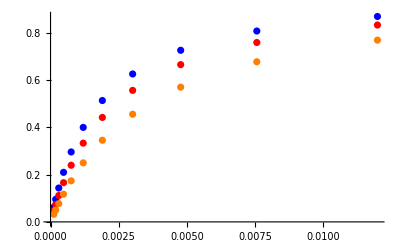

```mathematica
inhib1=inhibFittingData[[1;;11,{3,-1}]];
inhib2=inhibFittingData[[12;;22,{3,-1}]];
inhib3=inhibFittingData[[23;;33,{3,-1}]];
ListPlot[{inhib1, inhib2, inhib3}, PlotStyle->{Blue,Red, Orange}]
```

{1.,0.0018}

{1.,0.0024}

{1.,0.0036}

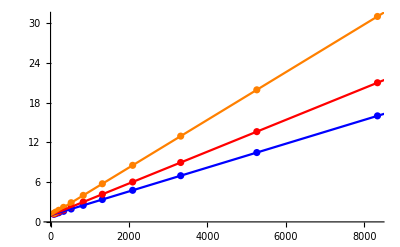

```mathematica
lm1=LinearModelFit[Map[{1/#[[1]],1/#[[2]]}&,inhib1],x,x];
lm2=LinearModelFit[Map[{1/#[[1]],1/#[[2]]}&,inhib2],x,x];
lm3=LinearModelFit[Map[{1/#[[1]],1/#[[2]]}&,inhib3],x,x];
lm1["ParameterTableEntries"][[All,1]]
lm2["ParameterTableEntries"][[All,1]]
lm3["ParameterTableEntries"][[All,1]]
Show[ListPlot[{Map[{1/#[[1]],1/#[[2]]}&,inhib1], Map[{1/#[[1]],1/#[[2]]}&,inhib2],
Map[{1/#[[1]],1/#[[2]]}&,inhib3]}, PlotStyle->{Blue,Red, Orange}],
Plot[{lm1[x],lm2[x],lm3[x]},{x,0,10000}, PlotStyle->{Blue,Red, Orange}]]
```

```mathematica
Dimensions@allFittingData
```

{192,11}

### Simulate data with uncertainty

```mathematica
Export["TALA2SimulateDataWithUncertaintyArguments.mx",{nSamples,enzymeModel,dataFileName, haldaneDataList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  metSatForSub, metSatRevSub, otherParmsList,  bufferInfo, ionCharge, inputPath,  fileList, 
							fileListSub, eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
							metsSub, KeqName,allCatalyticReactions,nonCatalyticReactions,  unifiedRateConstList, eqRateConstSub, customRatiosDataList}, "MX"];

Export["TALA2SimulateDataWithUncertaintyResults.mx",{allFittingDataList, dataPathList, fileList, fileListSub},"MX"];
```

```mathematica
nSamples=10;
SeedRandom[1234];
{allFittingDataList, dataPathList, fileList, fileListSub}=simulateDataWithUncertainty[nSamples,enzymeModel,dataFileName, haldaneDataList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  metSatForSub, metSatRevSub, otherParmsList,  bufferInfo, ionCharge, inputPath,  fileList, 
							fileListSub, eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
							metsSub, KeqName,allCatalyticReactions,nonCatalyticReactions,  unifiedRateConstList, eqRateConstSub, customRatiosDataList];
```

{0.0166535,0.0166535,0.0166535,0.0166535}

{0.0166535,0.0166535,0.0166535,0.0166535}

{0.0166535,0.0166535,0.0166535,0.0166535}

«7 more identical outputs»

```mathematica
FilePrint[dataPathList[[1]]]
```

e4p[c]	f6p[c]	g3p[c]	s7p[c]	pi[c]	param_TALA2_total	param_pH	param_Temp	FileFlag	Target_Data
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/haldaneRatio_1.txt"	0.7976188652987861
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/haldaneRatio_1.txt"	0.7976188652987861
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/haldaneRatio_1.txt"	0.7976188652987861
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/haldaneRatio_1.txt"	0.7976188652987861
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/haldaneRatio_1.txt"	0.7976188652987861
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/haldaneRatio_1.txt"	0.7976188652987861
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/haldaneRatio_1.txt"	0.7976188652987861
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/haldaneRatio_1.txt"	0.7976188652987861
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/haldaneRatio_1.txt"	0.7976188652987861
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/haldaneRatio_1.txt"	0.7976188652987861
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/haldaneRatio_1.txt"	0.7976188652987861
0	0	3.4971596682114973e-6	0.01	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_g3p.txt"	0.09090909090909086
0	0	5.542624551097971e-6	0.01	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_g3p.txt"	0.13680688860320997
0	0	8.784467919403012e-6	0.01	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_g3p.txt"	0.20076000891310178
0	0	0.000013922443404854854	0.01	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_g3p.txt"	0.28474724895080117
0	0	0.000022065585774779593	0.01	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_g3p.txt"	0.3868631798468568
0	0	0.00003497159668211497	0.01	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_g3p.txt"	0.4999999999999998
0	0	0.00005542624551097971	0.01	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_g3p.txt"	0.613136820153143
0	0	0.00008784467919403013	0.01	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_g3p.txt"	0.7152527510491986
0	0	0.00013922443404854867	0.01	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_g3p.txt"	0.7992399910868981
0	0	0.00022065585774779593	0.01	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_g3p.txt"	0.8631931113967898
0	0	0.00034971596682114973	0.01	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_g3p.txt"	0.9090909090909091
0.000010205108679489661	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_e4p.txt"	0.09090909090909094
0.000016174007274448992	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_e4p.txt"	0.1368068886032101
0.000025634074024090747	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_e4p.txt"	0.20076000891310192
0.000040627269415825704	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_e4p.txt"	0.2847472489508017
0.00006438988272542566	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_e4p.txt"	0.386863179846857
0.0001020510867948966	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_e4p.txt"	0.5
0.00016174007274448994	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_e4p.txt"	0.6131368201531432
0.0002563407402409075	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_e4p.txt"	0.7152527510491988
0.00040627269415825665	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_e4p.txt"	0.7992399910868984
0.0006438988272542565	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_e4p.txt"	0.86319311139679
0.001020510867948966	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_e4p.txt"	0.9090909090909092
0.01	0.00012062499333542214	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_f6p.txt"	0.0909090909090909
0.01	0.00019117773077797782	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_f6p.txt"	0.13680688860321003
0.01	0.00030299628406018036	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_f6p.txt"	0.2007600089131017
0.01	0.0004802167479479938	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_f6p.txt"	0.28474724895080145
0.01	0.0007610922547285893	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_f6p.txt"	0.38686317984685686
0.01	0.0012062499333542213	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_f6p.txt"	0.4999999999999999
0.01	0.0019117773077797781	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_f6p.txt"	0.6131368201531431
0.01	0.0030299628406018067	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_f6p.txt"	0.7152527510491987
0.01	0.004802167479479938	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_f6p.txt"	0.7992399910868982
0.01	0.007610922547285893	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_f6p.txt"	0.8631931113967899
0.01	0.012062499333542214	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_f6p.txt"	0.9090909090909091
0	0	0.01	0.000028550945785075704	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_s7p.txt"	0.0909090909090909
0	0	0.01	0.00004525019961309282	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_s7p.txt"	0.13680688860321005
0	0	0.01	0.00007171673332429735	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_s7p.txt"	0.20076000891310186
0	0	0.01	0.00011366336243122789	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_s7p.txt"	0.28474724895080145
0	0	0.01	0.00018014428934949323	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_s7p.txt"	0.3868631798468568
0	0	0.01	0.000285509457850757	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_s7p.txt"	0.4999999999999999
0	0	0.01	0.00045250199613092824	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_s7p.txt"	0.6131368201531431
0	0	0.01	0.0007171673332429736	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_s7p.txt"	0.7152527510491988
0	0	0.01	0.001136633624312279	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_s7p.txt"	0.7992399910868984
0	0	0.01	0.0018014428934949324	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_s7p.txt"	0.8631931113967899
0	0	0.01	0.0028550945785075703	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_s7p.txt"	0.9090909090909092
0.002	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	74.73681542932354
0.002	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	74.73681542932354
0.002	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	74.73681542932354
0.002	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	74.73681542932354
0.002	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	74.73681542932354
0.002	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	74.73681542932354
0.002	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	74.73681542932354
0.002	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	74.73681542932354
0.002	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	74.73681542932354
0.002	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	74.73681542932354
0.002	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	74.73681542932354
0.01	0.05	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	79.03887695340406
0.01	0.05	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	79.03887695340406
0.01	0.05	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	79.03887695340406
0.01	0.05	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	79.03887695340406
0.01	0.05	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	79.03887695340406
0.01	0.05	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	79.03887695340406
0.01	0.05	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	79.03887695340406
0.01	0.05	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	79.03887695340406
0.01	0.05	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	79.03887695340406
0.01	0.05	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	79.03887695340406
0.01	0.05	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	79.03887695340406
0.01	0.00011999999999999995	0	0	0.008954707009168561	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.06249999999999998
0.01	0.00037947331922020535	0	0	0.008954707009168561	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.1741123948954683
0.01	0.0011999999999999995	0	0	0.008954707009168561	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.3999999999999999
0.01	0.003794733192202054	0	0	0.008954707009168561	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.6782688399674104
0.01	0.011999999999999995	0	0	0.008954707009168561	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.8695652173913043
0.01	0.00011999999999999995	0	0	0.017909414018337122	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.0476190476190476
0.01	0.00037947331922020535	0	0	0.017909414018337122	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.13652705949581428
0.01	0.0011999999999999995	0	0	0.017909414018337122	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.33333333333333326
0.01	0.003794733192202054	0	0	0.017909414018337122	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.6125741132772069
0.01	0.011999999999999995	0	0	0.017909414018337122	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.8333333333333333
0.01	0.00011999999999999995	0	0	0.035818828036674244	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.03225806451612902
0.01	0.00037947331922020535	0	0	0.035818828036674244	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.09535767393825996
0.01	0.0011999999999999995	0	0	0.035818828036674244	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.2499999999999999
0.01	0.003794733192202054	0	0	0.035818828036674244	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.513167019494862
0.01	0.011999999999999995	0	0	0.035818828036674244	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.769230769230769
9.000000000000007e-6	0.01	0	0	0.008954707009168561	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.06250000000000004
0.000028460498941515435	0.01	0	0	0.008954707009168561	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.17411239489546843
0.00009000000000000007	0.01	0	0	0.008954707009168561	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.40000000000000013
0.00028460498941515434	0.01	0	0	0.008954707009168561	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.6782688399674106
0.0009000000000000007	0.01	0	0	0.008954707009168561	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.8695652173913043
9.000000000000007e-6	0.01	0	0	0.017909414018337122	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.04761904761904766
0.000028460498941515435	0.01	0	0	0.017909414018337122	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.1365270594958144
0.00009000000000000007	0.01	0	0	0.017909414018337122	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.33333333333333354
0.00028460498941515434	0.01	0	0	0.017909414018337122	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.612574113277207
0.0009000000000000007	0.01	0	0	0.017909414018337122	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.8333333333333336
9.000000000000007e-6	0.01	0	0	0.035818828036674244	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.03225806451612906
0.000028460498941515435	0.01	0	0	0.035818828036674244	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.09535767393826003
0.00009000000000000007	0.01	0	0	0.035818828036674244	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.25000000000000017
0.00028460498941515434	0.01	0	0	0.035818828036674244	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.5131670194948621
0.0009000000000000007	0.01	0	0	0.035818828036674244	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.7692307692307694
0	0	0.01	0.0000285	0.008954707009168561	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.06250000000000001
0	0	0.01	0.00009012491331479881	0.008954707009168561	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.17411239489546834
0	0	0.01	0.000285	0.008954707009168561	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.39999999999999997
0	0	0.01	0.0009012491331479881	0.008954707009168561	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.6782688399674105
0	0	0.01	0.00285	0.008954707009168561	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.8695652173913043
0	0	0.01	0.0000285	0.017909414018337122	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.04761904761904762
0	0	0.01	0.00009012491331479881	0.017909414018337122	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.13652705949581434
0	0	0.01	0.000285	0.017909414018337122	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.3333333333333333
0	0	0.01	0.0009012491331479881	0.017909414018337122	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.6125741132772069
0	0	0.01	0.00285	0.017909414018337122	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.8333333333333333
0	0	0.01	0.0000285	0.035818828036674244	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.03225806451612904
0	0	0.01	0.00009012491331479881	0.035818828036674244	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.09535767393825997
0	0	0.01	0.000285	0.035818828036674244	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.25
0	0	0.01	0.0009012491331479881	0.035818828036674244	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.513167019494862
0	0	0.01	0.00285	0.035818828036674244	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.7692307692307693
0	0	3.7999999999999996e-6	0.01	0.008954707009168561	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.062499999999999986
0	0	0.000012016655108639841	0.01	0.008954707009168561	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.17411239489546834
0	0	0.000037999999999999995	0.01	0.008954707009168561	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.3999999999999999
0	0	0.0001201665510863984	0.01	0.008954707009168561	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.6782688399674105
0	0	0.00037999999999999997	0.01	0.008954707009168561	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.8695652173913043
0	0	3.7999999999999996e-6	0.01	0.017909414018337122	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.04761904761904761
0	0	0.000012016655108639841	0.01	0.017909414018337122	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.1365270594958143
0	0	0.000037999999999999995	0.01	0.017909414018337122	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.33333333333333326
0	0	0.0001201665510863984	0.01	0.017909414018337122	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.6125741132772068
0	0	0.00037999999999999997	0.01	0.017909414018337122	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.8333333333333334
0	0	3.7999999999999996e-6	0.01	0.035818828036674244	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.032258064516129024
0	0	0.000012016655108639841	0.01	0.035818828036674244	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.09535767393825997
0	0	0.000037999999999999995	0.01	0.035818828036674244	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.24999999999999997
0	0	0.0001201665510863984	0.01	0.035818828036674244	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.5131670194948619
0	0	0.00037999999999999997	0.01	0.035818828036674244	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.7692307692307692
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/inhibRatio_pi.txt"	0.017909414018337122
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/inhibRatio_pi.txt"	0.017909414018337122
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/inhibRatio_pi.txt"	0.017909414018337122
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/inhibRatio_pi.txt"	0.017909414018337122
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/inhibRatio_pi.txt"	0.017909414018337122
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/inhibRatio_pi.txt"	0.017909414018337122
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/inhibRatio_pi.txt"	0.017909414018337122
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/inhibRatio_pi.txt"	0.017909414018337122
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/inhibRatio_pi.txt"	0.017909414018337122
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/inhibRatio_pi.txt"	0.017909414018337122
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/inhibRatio_pi.txt"	0.017909414018337122
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/customRatio_1.txt"	125.79
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/customRatio_1.txt"	125.79
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/customRatio_1.txt"	125.79
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/customRatio_1.txt"	125.79
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/customRatio_1.txt"	125.79
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/customRatio_1.txt"	125.79
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/customRatio_1.txt"	125.79
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/customRatio_1.txt"	125.79
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/customRatio_1.txt"	125.79
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/customRatio_1.txt"	125.79
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/customRatio_1.txt"	125.79

```mathematica
inhibitionList
```

{{Kic,pi,0.019,{0.016,0.022},{},{{Competitive,f6p,0.0012},{Competitive,e4p,0.00009},{Competitive,s7p,0.000285},{Competitive,g3p,0.000038}},M,8.5,30,{{glygly,0.05}},{}}}

### Parameter scan

```mathematica
Export["TALA2ParameterScanArguments.mx",{paramScanList, enzymeModel, dataFileName, 
						  haldaneDataList, kmList, s05List, kcatList, inhibitionList, activationList, 
						  otherParmsList, rxn, metsFull, metSatForSub, metSatRevSub,  bufferInfo, 
						  ionCharge, inputPath, fileList, fileListSub, eqnNameList, 
						  eqnValList, eqnValListPy, eqnNameList, rateConstsSub, metsSub, allCatalyticReactions,
						  nonCatalyticReactions, unifiedRateConstList, eqRateConstSub, customRatiosDataList}, "MX"];

Export["TALA2ParameterScanResults.mx",{allFittingDataList, dataPathList, fileList, fileListSub},"MX"];
```

```mathematica
Get["MASSef`"];
Get["MASSef`"];
paramScanList={{"Km",1,{0.1,1,100}},
				{"Km",2,{0.01,1,100}},
				{"Km",3,{0.01,10,100}},
				{"kcat",1,{0.01,1,100}},
				{"inhib",1,{10^-8,10.^-6,10^-4}}};

{allFittingDataList, dataPathList, fileList, fileListSub}=simulateParameterScanData[paramScanList, enzymeModel, dataFileName, 
						  haldaneDataList, kmList, s05List, kcatList, inhibitionList, activationList, 
						  otherParmsList, rxn, metsFull, metSatForSub, metSatRevSub,  bufferInfo, 
						  ionCharge, inputPath, fileList, fileListSub, eqnNameList, 
						  eqnValList, eqnValListPy, eqnNameList, rateConstsSub, metsSub, allCatalyticReactions,
						  nonCatalyticReactions, unifiedRateConstList, eqRateConstSub, customRatiosDataList];
```

{0.0166535,0.0166535,0.0166535,0.0166535}

{0.0166535,0.0166535,0.0166535,0.0166535}

{0.0166535,0.0166535,0.0166535,0.0166535}

«12 more identical outputs»

## Configure the Particle Swarm Optimization and Levenberg-Marquardt Algorithm

```mathematica
numTrials=1;
{psoParameterPath,psoResultsFileName, psoTrialSummaryFileName}  = definePSOparameters[inputPath, outputPath, finalRateConsts, fileList, numTrials,lowerParamBound, upperParamBound, fitLabel];
{lmaParameterPath, lmaResultsFileName} = defineLMAparameters[inputPath, outputPath, finalRateConsts, fileList, lowerParamBound, upperParamBound, fitLabel];
```

```mathematica
(*Print the Parameter File (Optional) *)
FilePrint[psoParameterPath]
```

num_Cpus	1
temperature_correction	False
num_trial	1
num_generations	2000
val_pop_size	20
bestFitnessCutoff	1.1
val_neigh_size	3
val_inertia	1
val_cogn_rate	2.1
val_soc_rate	2.1
use_Keep_Best	True
use_Random_Replace	True
percent_Rand	0.05
lower_bound	-6
upper_bound	9
num_func_var	14
filesWithFunctions	[/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_e4p.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_f6p.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_g3p.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_s7p.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/haldaneRatio_1.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/pi_inhibRatio.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/customRatio_1.txt]
value_row	-1
function_row	-2
data_row_high	-2

```mathematica
(*Optional*)
FilePrint[lmaParameterPath]
```

num_Cpus	1
temperature_correction	False
xtol_value	1.e-15
ftol_value	1.e-7
gtol_value	1.e-7
epsfcn_min_value	7
maxfev_value	1000
lower_bound	-6
upper_bound	9
num_func_var	14
filesWithFunctions	[/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_e4p.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_f6p.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_g3p.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_s7p.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/haldaneRatio_1.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/pi_inhibRatio.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/customRatio_1.txt]
value_row	-1
function_row	-2
data_row_high	-2

## Run the Fitting Algorithms

### Run Fitting on your Local System

```mathematica
runFitScriptPath= FileNameJoin[{pathMASSFittingPackage <> "python_code","src", "run_fit_rel.py"}, OperatingSystem->$OperatingSystem];

runPythonCmd =StringRiffle[{"python","\""<>runFitScriptPath <>"\"", "\""<>psoParameterPath <>"\"", "\""<>lmaParameterPath <>"\"", "\""<>psoTrialSummaryFileName <>"\"","\""<> psoResultsFileName <>"\"", "\""<>lmaResultsFileName <>"\"", ToString @numTrials, "\""<>dataPath <>"\""}, " "];

runBothCmd="cd \""<>inputPath<>"\" && "<>runPythonCmd;
runBothExe="!"<>runBothCmd <>" 2>&1";

Import[runBothExe<>" 2>&1","Text"]
```

best_fit: 2.91914995435
best_fit: 1.04897924636
best_fit: 1.01249180433
best_fit: 0.938261590057
best_fit: 0.838935927002

### Run Fitting on your Local System with uncertainty

```mathematica
Do[
runFitScriptPath= FileNameJoin[{pathMASSFittingPackage <> "python_code","src", "run_fit_rel.py"}, OperatingSystem->$OperatingSystem];

runPythonCmd =StringRiffle[{"python",
						"\""<>runFitScriptPath <>"\"",
						 "\""<>psoParameterPath <>"\"",
						 "\""<>lmaParameterPath <>"\"", 
						"\""<> StringTake[psoTrialSummaryFileName, ;;-5] <>"_"<>ToString[datasetI] <>".txt\"",
						"\""<> StringTake[psoResultsFileName, ;;-5] <>"_"<>ToString[datasetI] <>".txt\"",
						 "\""<>StringTake[lmaResultsFileName,;;-5]<>"_"<>ToString[datasetI] <>".txt\"", ToString @numTrials, 
						"\""<>dataPathList[[datasetI]] <>"\""}, " "];

runBothCmd="cd \""<>inputPath<>"\" && "<>runPythonCmd;
runBothExe="!"<>runBothCmd <>" 2>&1";

Import[runBothExe<>" 2>&1","Text"] ,

{datasetI, 1, Length@dataPathList}];
```

## Pull in Parameters and Check Fit and Enzyme Statistics

```mathematica
lmaResultsFileNameOld=lmaResultsFileName;
lmaResultsFileName=StringTake[lmaResultsFileNameOld,;;-5]<>"_"<>ToString[1] <>".txt\""
```

```mathematica
splitChar = If[$OperatingSystem == "Windows", "\\", "/"];
resultsFileName = StringSplit[lmaResultsFileName, splitChar][[-1]];
fittingData = Import[dataPath];
fittingData = fittingData[[2;;,All]];
resultsFile = FileNameJoin[{"raw",resultsFileName}, OperatingSystem->$OperatingSystem];
flagFitType = "abs_ssd";

{flagFitLocal, msgLocal, filteredDataList, bestFitDetails}=getRatesWithSSD[resultsFile, rxnName, fittingData, inputPath, outputPath,  fileListSub, rateConstsSub, metsSub, flagFitType, {}, False,fitLabel];
```

```mathematica
bestFitDetails//TableForm
```

Fitting Equation | Residual | Residual^2 | Relative error | True value | Predicted Value
 |  |  |  |  | 
haldaneRatio_1 | 0.0258633 | 0.000668908 | 5.78138 | 0.840336 | 0.791753
haldaneRatio_1 | 0.0258633 | 0.000668908 | 5.78138 | 0.840336 | 0.791753
haldaneRatio_1 | 0.0258633 | 0.000668908 | 5.78138 | 0.840336 | 0.791753
haldaneRatio_1 | 0.0258633 | 0.000668908 | 5.78138 | 0.840336 | 0.791753
haldaneRatio_1 | 0.0258633 | 0.000668908 | 5.78138 | 0.840336 | 0.791753
haldaneRatio_1 | 0.0258633 | 0.000668908 | 5.78138 | 0.840336 | 0.791753
haldaneRatio_1 | 0.0258633 | 0.000668908 | 5.78138 | 0.840336 | 0.791753
haldaneRatio_1 | 0.0258633 | 0.000668908 | 5.78138 | 0.840336 | 0.791753
haldaneRatio_1 | 0.0258633 | 0.000668908 | 5.78138 | 0.840336 | 0.791753
haldaneRatio_1 | 0.0258633 | 0.000668908 | 5.78138 | 0.840336 | 0.791753
haldaneRatio_1 | 0.0258633 | 0.000668908 | 5.78138 | 0.840336 | 0.791753
relRateRev_g3p | 0.0235028 | 0.00055238 | 5.56082 | 0.0909091 | 0.0959644
relRateRev_g3p | 0.0222852 | 0.000496629 | 5.26529 | 0.136807 | 0.14401
relRateRev_g3p | 0.0205943 | 0.000424125 | 4.85624 | 0.20076 | 0.210509
relRateRev_g3p | 0.0183837 | 0.000337959 | 4.32387 | 0.284747 | 0.297059
relRateRev_g3p | 0.015711 | 0.000246834 | 3.68381 | 0.386863 | 0.401114
relRateRev_g3p | 0.0127689 | 0.000163044 | 2.98379 | 0.5 | 0.514919
relRateRev_g3p | 0.00984656 | 0.0000969548 | 2.29315 | 0.613137 | 0.627197
relRateRev_g3p | 0.00722571 | 0.0000522109 | 1.6777 | 0.715253 | 0.727253
relRateRev_g3p | 0.00508193 | 0.000025826 | 1.17703 | 0.79924 | 0.808647
relRateRev_g3p | 0.00345659 | 0.000011948 | 0.799086 | 0.863193 | 0.870091
relRateRev_g3p | 0.00229386 | 5.2618×10^-6 | 0.529578 | 0.909091 | 0.913905
relRateFor_e4p | 0.504833 | 0.254856 | 219.766 | 0.0909091 | 0.290697
relRateFor_e4p | 0.459136 | 0.210806 | 187.83 | 0.136807 | 0.393771
relRateFor_e4p | 0.402551 | 0.162047 | 152.668 | 0.20076 | 0.507257
relRateFor_e4p | 0.337932 | 0.114198 | 117.737 | 0.284747 | 0.62
relRateFor_e4p | 0.270455 | 0.0731459 | 86.4039 | 0.386863 | 0.721128
relRateFor_e4p | 0.206209 | 0.0425222 | 60.7715 | 0.5 | 0.803858
relRateFor_e4p | 0.150254 | 0.0225762 | 41.3364 | 0.613137 | 0.866585
relRateFor_e4p | 0.105279 | 0.0110837 | 27.4321 | 0.715253 | 0.911462
relRateFor_e4p | 0.0714886 | 0.00511062 | 17.8932 | 0.79924 | 0.942249
relRateFor_e4p | 0.0474138 | 0.00224807 | 11.5357 | 0.863193 | 0.962768
relRateFor_e4p | 0.0309231 | 0.000956236 | 7.37992 | 0.909091 | 0.976181
relRateFor_f6p | 0.0362951 | 0.00131734 | 8.01757 | 0.0909091 | 0.0836204
relRateFor_f6p | 0.0345336 | 0.00119257 | 7.64372 | 0.136807 | 0.12635
relRateFor_f6p | 0.0320671 | 0.0010283 | 7.11772 | 0.20076 | 0.18647
relRateFor_f6p | 0.0288066 | 0.000829819 | 6.41776 | 0.284747 | 0.266473
relRateFor_f6p | 0.024809 | 0.000615485 | 5.55238 | 0.386863 | 0.365383
relRateFor_f6p | 0.0203365 | 0.000413575 | 4.57472 | 0.5 | 0.477126
relRateFor_f6p | 0.0158176 | 0.000250195 | 3.5766 | 0.613137 | 0.591207
relRateFor_f6p | 0.011698 | 0.000136844 | 2.65762 | 0.715253 | 0.696244
relRateFor_f6p | 0.00828029 | 0.0000685632 | 1.88855 | 0.79924 | 0.784146
relRateFor_f6p | 0.00565966 | 0.0000320317 | 1.29473 | 0.863193 | 0.852017
relRateFor_f6p | 0.00376909 | 0.000014206 | 0.86411 | 0.909091 | 0.901235
relRateRev_s7p | 0.0227168 | 0.000516055 | 5.0963 | 0.0909091 | 0.0862761
relRateRev_s7p | 0.021598 | 0.000466472 | 4.85148 | 0.136807 | 0.13017
relRateRev_s7p | 0.0200341 | 0.000401366 | 4.50824 | 0.20076 | 0.191709
relRateRev_s7p | 0.0179718 | 0.000322985 | 4.0537 | 0.284747 | 0.273204
relRateRev_s7p | 0.015451 | 0.000238734 | 3.49519 | 0.386863 | 0.373342
relRateRev_s7p | 0.012641 | 0.000159796 | 2.86875 | 0.5 | 0.485656
relRateRev_s7p | 0.00981274 | 0.0000962899 | 2.23413 | 0.613137 | 0.599439
relRateRev_s7p | 0.00724404 | 0.0000524762 | 1.65417 | 0.715253 | 0.703421
relRateRev_s7p | 0.00511992 | 0.0000262136 | 1.17198 | 0.79924 | 0.789873
relRateRev_s7p | 0.00349549 | 0.0000122184 | 0.801635 | 0.863193 | 0.856273
relRateRev_s7p | 0.00232591 | 5.40984×10^-6 | 0.534128 | 0.909091 | 0.904235
absRateFor | 0.000027492 | 7.55811×10^-10 | 0.00633007 | 71.4 | 71.3955
absRateFor | 0.000027492 | 7.55811×10^-10 | 0.00633007 | 71.4 | 71.3955
absRateFor | 0.000027492 | 7.55811×10^-10 | 0.00633007 | 71.4 | 71.3955
absRateFor | 0.000027492 | 7.55811×10^-10 | 0.00633007 | 71.4 | 71.3955
absRateFor | 0.000027492 | 7.55811×10^-10 | 0.00633007 | 71.4 | 71.3955
absRateFor | 0.000027492 | 7.55811×10^-10 | 0.00633007 | 71.4 | 71.3955
absRateFor | 0.000027492 | 7.55811×10^-10 | 0.00633007 | 71.4 | 71.3955
absRateFor | 0.000027492 | 7.55811×10^-10 | 0.00633007 | 71.4 | 71.3955
absRateFor | 0.000027492 | 7.55811×10^-10 | 0.00633007 | 71.4 | 71.3955
absRateFor | 0.000027492 | 7.55811×10^-10 | 0.00633007 | 71.4 | 71.3955
absRateFor | 0.000027492 | 7.55811×10^-10 | 0.00633007 | 71.4 | 71.3955
absRateFor | 0.0000220626 | 4.86756×10^-10 | 0.00508022 | 79.4 | 79.404
absRateFor | 0.0000220626 | 4.86756×10^-10 | 0.00508022 | 79.4 | 79.404
absRateFor | 0.0000220626 | 4.86756×10^-10 | 0.00508022 | 79.4 | 79.404
absRateFor | 0.0000220626 | 4.86756×10^-10 | 0.00508022 | 79.4 | 79.404
absRateFor | 0.0000220626 | 4.86756×10^-10 | 0.00508022 | 79.4 | 79.404
absRateFor | 0.0000220626 | 4.86756×10^-10 | 0.00508022 | 79.4 | 79.404
absRateFor | 0.0000220626 | 4.86756×10^-10 | 0.00508022 | 79.4 | 79.404
absRateFor | 0.0000220626 | 4.86756×10^-10 | 0.00508022 | 79.4 | 79.404
absRateFor | 0.0000220626 | 4.86756×10^-10 | 0.00508022 | 79.4 | 79.404
absRateFor | 0.0000220626 | 4.86756×10^-10 | 0.00508022 | 79.4 | 79.404
absRateFor | 0.0000220626 | 4.86756×10^-10 | 0.00508022 | 79.4 | 79.404
absRateFor | 0.56141 | 0.315181 | 72.547 | 0.0625 | 0.0171581
absRateFor | 0.506769 | 0.256815 | 68.8663 | 0.174112 | 0.0542076
absRateFor | 0.369292 | 0.136376 | 57.2724 | 0.4 | 0.17091
absRateFor | 0.102694 | 0.0105461 | 21.0584 | 0.678269 | 0.535436
absRateFor | 0.276808 | 0.0766228 | 89.1508 | 0.869565 | 1.64479
absRateFor | 0.743794 | 0.553229 | 81.9613 | 0.047619 | 0.00858988
absRateFor | 0.701543 | 0.492162 | 80.1181 | 0.136527 | 0.0271441
absRateFor | 0.590185 | 0.348318 | 74.307 | 0.333333 | 0.0856434
absRateFor | 0.357556 | 0.127846 | 56.102 | 0.612574 | 0.268908
absRateFor | 0.000847954 | 7.19025×10^-7 | 0.195058 | 0.833333 | 0.831708
absRateFor | 0.875407 | 0.766338 | 86.6773 | 0.0322581 | 0.00429765
absRateFor | 0.846386 | 0.71637 | 85.7566 | 0.0953577 | 0.0135822
absRateFor | 0.765797 | 0.586446 | 82.8524 | 0.25 | 0.0428689
absRateFor | 0.58072 | 0.337235 | 73.7409 | 0.513167 | 0.134753
absRateFor | 0.26465 | 0.0700395 | 45.6311 | 0.769231 | 0.418222
absRateFor | 0.0178481 | 0.000318553 | 4.19529 | 0.0625 | 0.0651221
absRateFor | 0.031442 | 0.000988601 | 7.50831 | 0.174112 | 0.187185
absRateFor | 0.0603291 | 0.00363961 | 14.9024 | 0.4 | 0.45961
absRateFor | 0.0987779 | 0.00975708 | 25.5388 | 0.678269 | 0.85149
absRateFor | 0.127333 | 0.0162138 | 34.0706 | 0.869565 | 1.16583
absRateFor | 0.164408 | 0.02703 | 31.5156 | 0.047619 | 0.0326116
absRateFor | 0.162978 | 0.0265619 | 31.2897 | 0.136527 | 0.0938081
absRateFor | 0.159796 | 0.0255348 | 30.7844 | 0.333333 | 0.230719
absRateFor | 0.155241 | 0.0240997 | 30.0546 | 0.612574 | 0.428468
absRateFor | 0.151605 | 0.0229842 | 29.4666 | 0.833333 | 0.587778
absRateFor | 0.295958 | 0.0875912 | 49.4127 | 0.0322581 | 0.0163185
absRateFor | 0.307645 | 0.0946454 | 50.7558 | 0.0953577 | 0.0469581
absRateFor | 0.335023 | 0.11224 | 53.7644 | 0.25 | 0.115589
absRateFor | 0.37798 | 0.142869 | 58.1187 | 0.513167 | 0.214921
absRateFor | 0.416058 | 0.173104 | 61.6344 | 0.769231 | 0.29512
absRateRev | 0.730068 | 0.532999 | 81.382 | 0.0625 | 0.0116362
absRateRev | 0.675547 | 0.456363 | 78.8917 | 0.174112 | 0.0367522
absRateRev | 0.538446 | 0.289924 | 71.0563 | 0.4 | 0.115775
absRateRev | 0.273024 | 0.0745421 | 46.6695 | 0.678269 | 0.361724
absRateRev | 0.102921 | 0.0105927 | 26.7421 | 0.869565 | 1.10211
absRateRev | 0.91245 | 0.832565 | 87.7665 | 0.047619 | 0.00582547
absRateRev | 0.870315 | 0.757449 | 86.5202 | 0.136527 | 0.0184036
absRateRev | 0.759325 | 0.576574 | 82.5949 | 0.333333 | 0.0580169
absRateRev | 0.527843 | 0.278619 | 70.341 | 0.612574 | 0.181683
absRateRev | 0.174642 | 0.0304999 | 33.1105 | 0.833333 | 0.557412
absRateRev | 1.04406 | 1.09007 | 90.9648 | 0.0322581 | 0.00291458
absRateRev | 1.01516 | 1.03054 | 90.343 | 0.0953577 | 0.00920871
absRateRev | 0.93493 | 0.874094 | 88.3836 | 0.25 | 0.0290409
absRateRev | 0.750986 | 0.563981 | 82.2576 | 0.513167 | 0.0910484
absRateRev | 0.438397 | 0.192192 | 63.5579 | 0.769231 | 0.280324
absRateRev | 0.691793 | 0.478577 | 79.6667 | 0.0625 | 0.0127083
absRateRev | 0.639875 | 0.40944 | 77.0847 | 0.174112 | 0.0398983
absRateRev | 0.510865 | 0.260983 | 69.1585 | 0.4 | 0.123366
absRateRev | 0.269701 | 0.0727389 | 46.2599 | 0.678269 | 0.364502
absRateRev | 0.0404642 | 0.00163735 | 9.76508 | 0.869565 | 0.954479
absRateRev | 0.874171 | 0.764174 | 86.6393 | 0.047619 | 0.00636224
absRateRev | 0.834631 | 0.696609 | 85.3658 | 0.136527 | 0.0199796
absRateRev | 0.731713 | 0.535404 | 81.4524 | 0.333333 | 0.0618252
absRateRev | 0.52451 | 0.27511 | 70.1124 | 0.612574 | 0.183083
absRateRev | 0.237702 | 0.0565023 | 42.1507 | 0.833333 | 0.482077
absRateRev | 1.00578 | 1.0116 | 90.1322 | 0.0322581 | 0.00318315
absRateRev | 0.979466 | 0.959354 | 89.5158 | 0.0953577 | 0.00999746
absRateRev | 0.907303 | 0.823199 | 87.6207 | 0.25 | 0.0309483
absRateRev | 0.747647 | 0.558976 | 82.1206 | 0.513167 | 0.0917512
absRateRev | 0.501763 | 0.251766 | 68.5054 | 0.769231 | 0.242266
inhibRatio_pi | 2.93672 | 8.62433 | 99.8843 | 0.019 | 0.0000219802
inhibRatio_pi | 2.93672 | 8.62433 | 99.8843 | 0.019 | 0.0000219802
inhibRatio_pi | 2.93672 | 8.62433 | 99.8843 | 0.019 | 0.0000219802
inhibRatio_pi | 2.93672 | 8.62433 | 99.8843 | 0.019 | 0.0000219802
inhibRatio_pi | 2.93672 | 8.62433 | 99.8843 | 0.019 | 0.0000219802
inhibRatio_pi | 2.93672 | 8.62433 | 99.8843 | 0.019 | 0.0000219802
inhibRatio_pi | 2.93672 | 8.62433 | 99.8843 | 0.019 | 0.0000219802
inhibRatio_pi | 2.93672 | 8.62433 | 99.8843 | 0.019 | 0.0000219802
inhibRatio_pi | 2.93672 | 8.62433 | 99.8843 | 0.019 | 0.0000219802
inhibRatio_pi | 2.93672 | 8.62433 | 99.8843 | 0.019 | 0.0000219802
inhibRatio_pi | 2.93672 | 8.62433 | 99.8843 | 0.019 | 0.0000219802
customRatio_1 | 1.00677×10^-9 | 1.01359×10^-18 | 2.31817×10^-7 | 125.79 | 125.79
customRatio_1 | 1.00677×10^-9 | 1.01359×10^-18 | 2.31817×10^-7 | 125.79 | 125.79
customRatio_1 | 1.00677×10^-9 | 1.01359×10^-18 | 2.31817×10^-7 | 125.79 | 125.79
customRatio_1 | 1.00677×10^-9 | 1.01359×10^-18 | 2.31817×10^-7 | 125.79 | 125.79
customRatio_1 | 1.00677×10^-9 | 1.01359×10^-18 | 2.31817×10^-7 | 125.79 | 125.79
customRatio_1 | 1.00677×10^-9 | 1.01359×10^-18 | 2.31817×10^-7 | 125.79 | 125.79
customRatio_1 | 1.00677×10^-9 | 1.01359×10^-18 | 2.31817×10^-7 | 125.79 | 125.79
customRatio_1 | 1.00677×10^-9 | 1.01359×10^-18 | 2.31817×10^-7 | 125.79 | 125.79
customRatio_1 | 1.00677×10^-9 | 1.01359×10^-18 | 2.31817×10^-7 | 125.79 | 125.79
customRatio_1 | 1.00677×10^-9 | 1.01359×10^-18 | 2.31817×10^-7 | 125.79 | 125.79
customRatio_1 | 1.00677×10^-9 | 1.01359×10^-18 | 2.31817×10^-7 | 125.79 | 125.79

### Simulated Data and Best Fit Data Plot

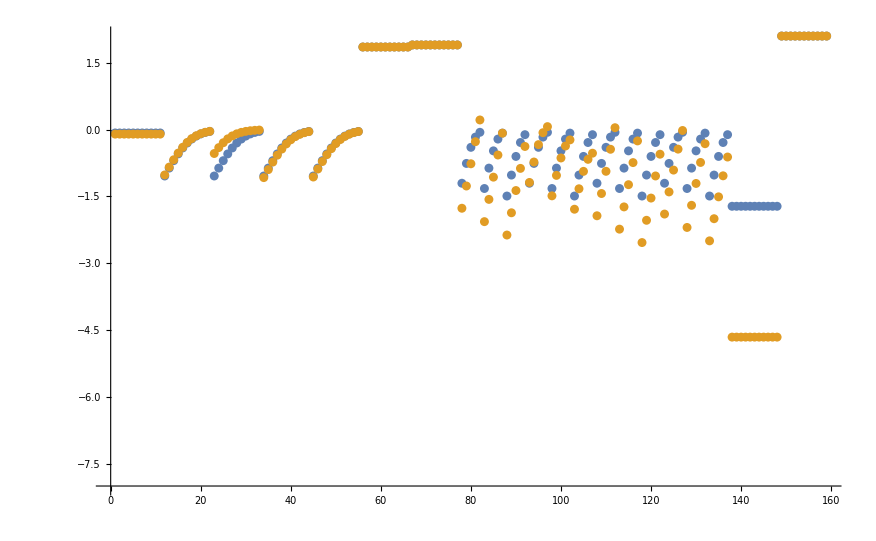

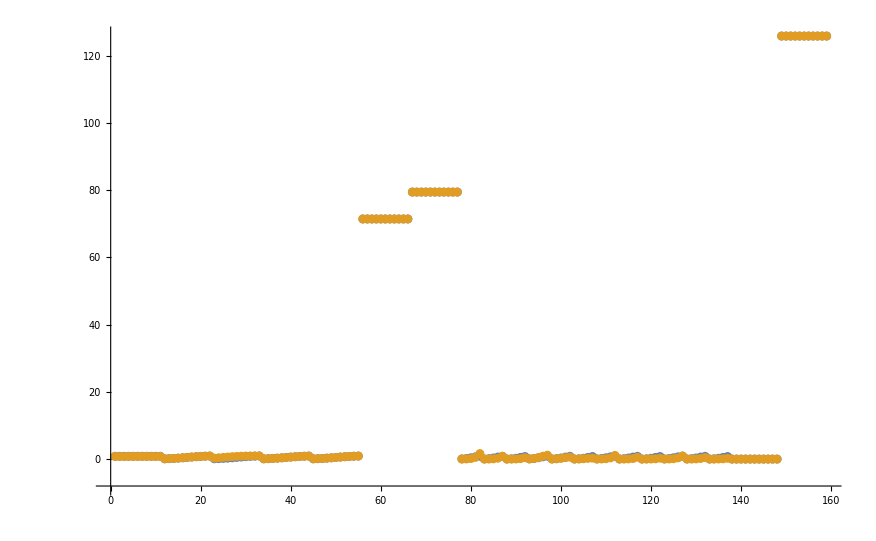

```mathematica
ListPlot[Log10[{fittingData[[All,-1]],filteredDataList[[1,3]]}], AxesOrigin->{0,-8}]
ListPlot[{fittingData[[All,-1]],filteredDataList[[1,3]]}, AxesOrigin->{0,-8}]
```

### Parameter Distribution

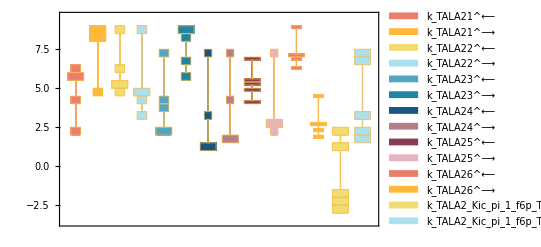

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartElementFunction->"HistogramDensity","PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24]
```

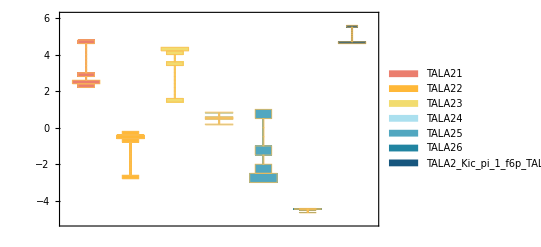

```mathematica
{ratios, plotLegend} = getElementaryKeqs[filteredDataList, rateConstsSub];
DistributionChart[Log10[Transpose@ratios],ChartElementFunction->"HistogramDensity",ChartLegends-> plotLegend,ChartStyle-> 24](*Histogram*)
```

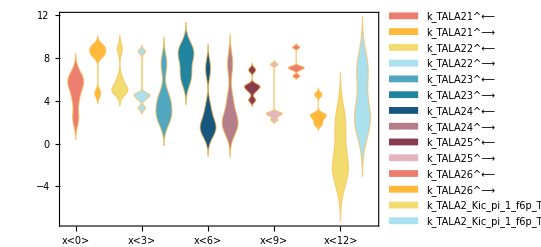

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartLabels-> rateConstsSub[[All,2]],"PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24](*Smooth*)(*If the distribution is narrow, the smooth Kernel outputs an error*)
```

### Data Error Distribution

```mathematica
errors=
Table[
	fittingData[[i,-1]]-filteredDataList[[j,3,i]],
 {j,1,Length@filteredDataList},{i,1,Length@filteredDataList[[1,3]]}];
```

```mathematica
funcNames=
Table[
	StringCases[func,RegularExpression[FileNameJoin[{inputPath , "(.*)\\.txt"}, OperatingSystem->$OperatingSystem]]->"$1"][[1]],{func,fittingData[[All,-2]]}]; (* fix later*);
```

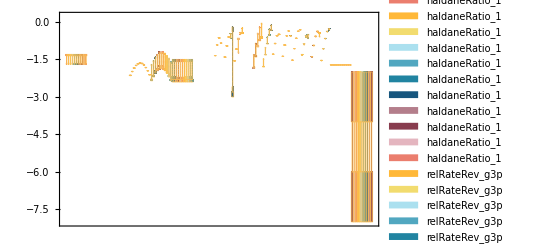

```mathematica
DistributionChart[Transpose[Log10[errors]],ChartElementFunction->"HistogramDensity",ChartLegends-> funcNames,ChartStyle-> 24](*Histogram*)
```

### Recalculate Enzyme Parameters for all Candidate Rate Constant Sets

```mathematica
enzymeSub= parameter[rxnName<>"_total"]-> 1;
assumedSaturatingConc=0.01;
paramSet = 1;
paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[paramSet,2]]];
```

```mathematica
backCalculateKms[rxn, kmList[[{1,2,4,5}]], absoluteRateForward/.m["pi","c"]-> 0, absoluteRateReverse/.m["pi","c"]-> 0, paramFitSub, assumedSaturatingConc, KeqName]//TableForm
```

data value | predicted value | error in %
0.000038 | 0.000035798 | 5.79467
0.00009 | 0.0000219601 | 75.5999
0.0012 | 0.00131506 | 9.58806
0.000285 | 0.000301835 | 5.90696

```mathematica
backCalculateKcats[rxn, kcatList,absoluteRateForward/.m["pi","c"]-> 0, absoluteRateReverse/.m["pi","c"]-> 0, paramFitSub, enzymeSub, assumedSaturatingConc]//TableForm
```

data value | predicted value | error in %
71.4 | 71.3955 | 0.00633007
79.4 | 71.3955 | 10.0813

```mathematica
backCalculateRatios[customRatiosList[[1]][[1]], customRatiosList[[1]][[2]], paramFitSub]//TableForm
```

data value | predicted value | error in %
125.79 | 125.79 | 2.31817×10^-7

```mathematica
backCalculateRatios[haldaneRatiosList[[1]][[1]], haldaneRatiosList[[1]][[2]], paramFitSub]//TableForm
```

data value | predicted value | error in %
0.840336 | 0.791753 | 5.78138